# 量子线路和量子模拟

## 魏文杰

## 癸卯年十月初七 2023年11月19日15:50:24

```mathematica
<<Wolfram`QuantumFramework`
```

## 目录

量子线路模型

单比特门

受控门

测量

通用量子门

总结：量子计算机的要素

其他量子计算模型

量子模拟

总结：需要记住的关键知识点

参考文献

## 1 量子线路模型 Quantum Circuit

本章将详细探讨量子计算，阐述量子计算的基本原理，建立量子电路的基本构造框架。
量子线路是一种描述复杂量子计算的通用语言。
目前已知的两个基础量子算法量子傅里叶变换、量子搜索算法是由这些电路在接下来两章中构造的。
逻辑门的列表

## 1.1 单比特门 U(2)

### X 门 和 R_X(θ)门

```mathematica
opx=QuantumOperator["X"];
opx=QuantumOperator[PauliMatrix[1]];
opx["Matrix"]//Normal//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
opx//TraditionalForm
```

01+10

```mathematica
(QuantumState/@(#/Norm[#]&/@Eigenvectors[PauliMatrix[1]]))//TraditionalForm
```

{-0/(√2)+1/(√2),0/(√2)+1/(√2)}

```mathematica
opx[QuantumState[{α,β}]]//TraditionalForm
```

β 0+α 1

```mathematica
QuantumOperator[{"RX",θ}]["Matrix"]//Normal//FullSimplify//MatrixForm
MatrixExp[-I θ/2 PauliMatrix[1]]//MatrixForm(*绕着x轴旋转角度θ*)
I %/.θ->Pi//MatrixForm
```

(Cos[θ/2] | -ⅈ Sin[θ/2]
-ⅈ Sin[θ/2] | Cos[θ/2])

(Cos[θ/2] | -ⅈ Sin[θ/2]
-ⅈ Sin[θ/2] | Cos[θ/2])

(0 | 1
1 | 0)

### Y 门 和 R_Y(θ)门

```mathematica
opy=QuantumOperator[PauliMatrix[2]];
opy["Matrix"]//Normal//MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
QuantumOperator[{"RY",θ}]["Matrix"]//Normal//FullSimplify//MatrixForm
MatrixExp[-I θ/2 PauliMatrix[2]]//MatrixForm
I %/.θ->Pi//MatrixForm
```

(Cos[θ/2] | -Sin[θ/2]
Sin[θ/2] | Cos[θ/2])

(Cos[θ/2] | -Sin[θ/2]
Sin[θ/2] | Cos[θ/2])

(0 | -ⅈ
ⅈ | 0)

### Z 门 和 R_Z(θ)门

```mathematica
QuantumCircuitOperator["Z"];
%["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | -1)

```mathematica
QuantumOperator["Z"]//TraditionalForm
```

00-11

```mathematica
QuantumOperator[{"RZ",θ}]["Matrix"]//Normal//FullSimplify//MatrixForm
MatrixExp[-I θ/2 PauliMatrix[3]]//MatrixForm
I %/.θ->Pi//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

(1 | 0
0 | -1)

-Graphics-

### R_n(θ) 门：绕着轴 n = (x,y,z) 旋转角度 θ

-Graphics-

```mathematica
n[i_]:={x,y,z}[[i]];
```

```mathematica
MatrixExp[-I θ/2 Sum[n[i] PauliMatrix[i],{i,3}]]//Simplify[#,{x,y,z}∈Sphere[]]&//FullSimplify//MatrixForm
```

(Cos[θ/2]-ⅈ z Sin[θ/2] | (-ⅈ x-y) Sin[θ/2]
(-ⅈ x+y) Sin[θ/2] | Cos[θ/2]+ⅈ z Sin[θ/2])

### Hadamard 门

```mathematica
H=QuantumCircuitOperator["H"];
%["Matrix"]//Normal//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
QuantumOperator["H"]//TraditionalForm
QuantumOperator["H"]@QuantumState[{1,0}]//TraditionalForm
QuantumOperator["H"]@QuantumState[{0,1}]//TraditionalForm
```

00/(√2)+01/(√2)+10/(√2)-11/(√2)

0/(√2)+1/(√2)

0/(√2)-1/(√2)

```mathematica
(H/*H)["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
H[QuantumState[{1,0}]]//TraditionalForm
H[QuantumState[{0,1}]]//TraditionalForm
```

0/(√2)+1/(√2)

0/(√2)-1/(√2)

用 H 门制作均匀(等系数)叠加态

```mathematica
QuantumCircuitOperator["HHH"][QuantumState[{1,0,0,0,0,0,0,0}]]//TraditionalForm
```

000/(2 √2)+001/(2 √2)+010/(2 √2)+011/(2 √2)+100/(2 √2)+101/(2 √2)+110/(2 √2)+111/(2 √2)

### 相位门 S

```mathematica
QuantumOperator["S"]["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | ⅈ)

### T 门

```mathematica
QuantumOperator["T"]["Matrix"]//Normal//MatrixForm
t=QuantumOperator["T"]["Matrix"]//Normal;
```

(1 | 0
0 | ⅇ^((ⅈ π)/4))

### 单比特门的一般性质

#### 将一个单比特门视为对qubit的一次旋转

任何单比特门(U(2))都是旋转R_n(θ)乘一个相位

-Graphics-

u ∈ U(2), 存在 s ∈ SU(2)，满足 u = e^(i α) s

s =Conjugate[√Det[u]] u

```mathematica
rnt2=MatrixExp[-I θ/2 Sum[n[i] PauliMatrix[i],{i,3}]]//Simplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
rnt2//MatrixForm
rnt2/.θ->2π
```

(Cos[θ/2]-ⅈ z Sin[θ/2] | (-ⅈ x-y) Sin[θ/2]
(-ⅈ x+y) Sin[θ/2] | Cos[θ/2]+ⅈ z Sin[θ/2])

{{-1,0},{0,-1}}

```mathematica
{{α,β},{-Conjugate[β],Conjugate[α]}}//MatrixForm
```

(α | β
-Conjugate[β] | Conjugate[α])

```mathematica
sol=Solve[rnt2=={{α,β},{-Conjugate[β],Conjugate[α]}},{θ,x,y,z}]//FullSimplify[#,C[1]==0&&0<θ<2π]&
```

{{x→(2 ⅈ (β-Re[β]))/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),y→-(2 Re[β])/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),z→(2 ⅈ (α-Re[α]))/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),θ→2 ArcTan[2 Re[α],√(4+α^2-Conjugate[α]^2-4 α Re[α])]},{x→-(2 ⅈ (β-Re[β]))/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),y→(2 Re[β])/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),z→-(2 ⅈ (α-Re[α]))/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),θ→2 ArcTan[2 Re[α],-√(4+α^2-Conjugate[α]^2-4 α Re[α])]}}

2. 哈达玛门

```mathematica
h=QuantumCircuitOperator["H"]["Matrix"]//Normal;
%//MatrixForm
Det[h]
sol/.{α->√Det[h] h[[1,1]],β->√Det[h] h[[1,2]]}
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

-1

{{x→-1/(√2),y→0,z→-1/(√2),θ→π},{x→1/(√2),y→0,z→1/(√2),θ→-π}}

3. 相位门

```mathematica
s=QuantumCircuitOperator["S"]["Matrix"]//Normal;
%//MatrixForm
Det[s]
sol/.{α->√(Conjugate@Det[s])s[[1,1]],β->√(Conjugate@Det[s])s[[1,2]]}//Simplify
```

(1 | 0
0 | ⅈ)

ⅈ

{{x→0,y→0,z→1,θ→π/2},{x→0,y→0,z→-1,θ→-π/2}}

```mathematica
√Det[s] MatrixExp[-I π/4 PauliMatrix[3]]//MatrixForm//Simplify(*验证解出来的n,θ和α确实能得到S*)
```

(1 | 0
0 | ⅈ)

3维与2维的旋转的联系

-Graphics-

-Graphics-

```mathematica
Clear[n]
```

```mathematica
n[i_]:={x,y,z}[[i]];(*转轴*)
```

```mathematica
rnt2=MatrixExp[-I θ/2 Sum[n[i] PauliMatrix[i],{i,3}]]//Simplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
%//MatrixForm
blc2={Cos[α/2],E^(I β)Sin[α/2]};(*变换前的qubit，α和β分别是Bloch矢量的极角与经度角*)
rp=rnt2.blc2//FullSimplify;
rp//MatrixForm
```

(Cos[θ/2]-ⅈ z Sin[θ/2] | (-ⅈ x-y) Sin[θ/2]
(-ⅈ x+y) Sin[θ/2] | Cos[θ/2]+ⅈ z Sin[θ/2])

((x-ⅈ y) Sin[α/2] (-ⅈ Cos[β]+Sin[β]) Sin[θ/2]+Cos[α/2] (Cos[θ/2]-ⅈ z Sin[θ/2])
(-ⅈ x+y) Cos[α/2] Sin[θ/2]+ⅇ^(ⅈ β) Sin[α/2] (Cos[θ/2]+ⅈ z Sin[θ/2]))

```mathematica
ρblc=KroneckerProduct[rp,ConjugateTranspose[rp]]//FullSimplify[#,(θ|α|β|z|x|y)∈Reals]&;(*变换后的态*)
```

```mathematica
blc3p=Table[Tr[ρblc.PauliMatrix[i]],{i,3}]//FullSimplify[#,{x,y,z}∈Sphere[]]&
```

{Cos[β] (1+y^2 (-1+Cos[θ])+z^2 (-1+Cos[θ])) Sin[α]-x (-1+Cos[θ]) (z Cos[α]+y Sin[α] Sin[β])+(y Cos[α]-z Sin[α] Sin[β]) Sin[θ],-Cos[α] (y z (-1+Cos[θ])+x Sin[θ])+Sin[α] ((y^2 (1-Cos[θ])+Cos[θ]) Sin[β]+Cos[β] (x y-x y Cos[θ]+z Sin[θ])),Cos[α] (z^2 (1-Cos[θ])+Cos[θ])+Sin[α] (-z (-1+Cos[θ]) (x Cos[β]+y Sin[β])+(-y Cos[β]+x Sin[β]) Sin[θ])}

```mathematica
Clear[m]
```

```mathematica
m[1]=I D[RotationMatrix[θ,{1,0,0}],θ]/.θ->0;
m[2]=I D[RotationMatrix[θ,{0,1,0}],θ]/.θ->0;
m[3]=I D[RotationMatrix[θ,{0,0,1}],θ]/.θ->0;
```

-Graphics-

```mathematica
rnt3=MatrixExp[-I θ Sum[n[i] m[i],{i,3}]]//FullSimplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
rnt3//MatrixForm
```

(1+y^2 (-1+Cos[θ])+z^2 (-1+Cos[θ]) | x y-x y Cos[θ]-z Sin[θ] | x z-x z Cos[θ]+y Sin[θ]
x y-x y Cos[θ]+z Sin[θ] | y^2+Cos[θ]-y^2 Cos[θ] | y z-y z Cos[θ]-x Sin[θ]
x z-x z Cos[θ]-y Sin[θ] | y z-y z Cos[θ]+x Sin[θ] | z^2+Cos[θ]-z^2 Cos[θ])

```mathematica
blc3=CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,α,β}]
```

{Cos[β] Sin[α],Sin[α] Sin[β],Cos[α]}

```mathematica
blc3pp=rnt3.blc3//FullSimplify[#,{x,y,z}∈Sphere[]]&;
%//MatrixForm(*旋转后的Bloch矢量*)
```

(Cos[α] (x z-x z Cos[θ]+y Sin[θ])+Sin[α] (Cos[β] (1+y^2 (-1+Cos[θ])+z^2 (-1+Cos[θ]))-Sin[β] (x y (-1+Cos[θ])+z Sin[θ]))
(y^2 (1-Cos[θ])+Cos[θ]) Sin[α] Sin[β]-Cos[α] (y z (-1+Cos[θ])+x Sin[θ])+Cos[β] Sin[α] (x y-x y Cos[θ]+z Sin[θ])
Cos[α] (z^2 (1-Cos[θ])+Cos[θ])+Sin[α] (-z (-1+Cos[θ]) (x Cos[β]+y Sin[β])+(-y Cos[β]+x Sin[β]) Sin[θ]))

```mathematica
blc3pp-blc3p//FullSimplify[#,{x,y,z}∈Sphere[]]&//MatrixForm
```

(0
0
0)

用类似的方法可以完成下面的习题

-Graphics-

不失一般性，假设转轴沿着 z 方向

```mathematica
rnt2=MatrixExp[-I θ/2 PauliMatrix[3]]//Simplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
%//MatrixForm
blc2={Cos[α/2],E^(I β)Sin[α/2]};(*变换前的qubit，α和β分别是Bloch矢量的极角与经度角*)
rp=rnt2.blc2//FullSimplify;
rp//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

(ⅇ^(-(ⅈ θ)/2) Cos[α/2]
ⅇ^(1/2 ⅈ (2 β+θ)) Sin[α/2])

```mathematica
ρblc=KroneckerProduct[rp,ConjugateTranspose[rp]]//FullSimplify[#,(θ|α|β|z|x|y)∈Reals]&;(*变换后的态*)
```

```mathematica
blc3p=Table[Tr[ρblc.PauliMatrix[i]],{i,3}]//FullSimplify[#,{x,y,z}∈Sphere[]]&
```

{Cos[β+θ] Sin[α],Sin[α] Sin[β+θ],Cos[α]}

```mathematica
m[3]=I D[RotationMatrix[θ,{0,0,1}],θ]/.θ->0;
```

-Graphics-

```mathematica
rnt3=MatrixExp[-I θ  m[3]]//FullSimplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
rnt3//MatrixForm
```

(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)

```mathematica
blc3=CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,α,β}]
```

{Cos[β] Sin[α],Sin[α] Sin[β],Cos[α]}

```mathematica
blc3pp=rnt3.blc3//FullSimplify[#,{x,y,z}∈Sphere[]]&;
%//MatrixForm(*旋转后的Bloch矢量*)
```

(Cos[β+θ] Sin[α]
Sin[α] Sin[β+θ]
Cos[α])

```mathematica
blc3pp-blc3p//FullSimplify[#,{x,y,z}∈Sphere[]]&//MatrixForm
```

(0
0
0)

如何理解发生在Hilbert空间中的旋转？

量子现象发生在实验室的仪器中，与我们生活在相同的宇宙中，而不是发生在希尔伯特空间中，当粒子的z方向自旋角动量为 ℏ/2，即粒子处于|0⟩态，然后我们建立新坐标系使得新的 x’ 轴与原来的z轴重合，那么新的量子态有确定的x方向自旋角动量，态应该变为|+⟩

描述因为旋转参考系空间的导致的态的变换，需要使用SO(3)的以单比特希尔伯特空间为表示空间的某个群表示，即SU(2)

SO(3)作用在3维线性空间上，SU(2)作用在2维希尔伯特空间上，群作用的概念使得我们能将旋转的概念从3维的实空间迁移到qubit生活的希尔伯特空间上。

演示 the Belt Trick1-2

-Graphics-

#### 将单比特门视为三次旋转的复合：单比特门的 z-y-z 分解与欧拉角

-Graphics-

用U(1)门与R_Z(θ), R_Y(θ)可以生成所有单比特门

```mathematica
QuantumOperator[{"U3",θ,β,δ}]["Matrix"]//Normal//MatrixForm
```

(Cos[θ/2] | -ⅇ^(ⅈ δ) Sin[θ/2]
ⅇ^(ⅈ β) Sin[θ/2] | ⅇ^(ⅈ (β+δ)) Cos[θ/2])

```mathematica
zyz=ⅇ^(1/2 ⅈ (β+δ)) QuantumOperator[{"RZ",β}]@QuantumOperator[{"RY",θ}]@QuantumOperator[{"RZ",δ}];
u3=zyz["Matrix"]//Normal//FullSimplify(*定理4.1*);u3//MatrixForm(*根据矩阵确定转轴和转角?*)
```

(Cos[θ/2] | -ⅇ^(ⅈ δ) Sin[θ/2]
ⅇ^(ⅈ β) Sin[θ/2] | Cos[θ/2] (Cos[β+δ]+ⅈ Sin[β+δ]))

```mathematica
Det[u3]//Simplify
```

Cos[β+δ]+ⅈ Sin[β+δ]

```mathematica
RollPitchYawMatrix[{α,β,γ},{1,2,3}]-EulerMatrix[{γ,β,α},{1,2,3}]//FullSimplify
```

{{Cos[β] (-Cos[α]+Cos[γ]),Sin[α] (Cos[β]+Cos[γ] Sin[β])-Cos[α] Sin[γ],(-1+Cos[α] Cos[γ]) Sin[β]+Sin[α] Sin[γ]},{-Cos[γ] Sin[α]+(Cos[β]-Cos[α] Sin[β]) Sin[γ],2 Sin[α] Sin[β] Sin[γ],-Cos[γ] Sin[α]+(Cos[β]+Cos[α] Sin[β]) Sin[γ]},{(-1+Cos[α] Cos[γ]) Sin[β]-Sin[α] Sin[γ],Sin[α] (Cos[β]-Cos[γ] Sin[β])-Cos[α] Sin[γ],Cos[β] (Cos[α]-Cos[γ])}}

```mathematica
RollPitchYawMatrix[{α,β,γ},{1,2,3}]==EulerMatrix[{γ,β,α},{3,2,1}]
```

True

-Graphics-

```mathematica
(ⅇ^(1/2 ⅈ (π)) QuantumOperator[{"RZ",π/2}]@QuantumOperator[{"RX",π/2}]@QuantumOperator[{"RZ",π/2}])["Matrix"]//Normal//Simplify//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

将H分解成Ry、Rz和相位因子的积

```mathematica
ls=QuantumOperator["H"]["ZYZ"]//QuantumShortcut
QuantumOperator[%]["Matrix"]//Normal//MatrixForm
```

{{U,π/2,0,π}→{1}}

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
(ⅇ^(ⅈ (π)/2) QuantumOperator[{"RZ",0}]@QuantumOperator[{"RY",π/2}]@QuantumOperator[{"RZ",π}])["Matrix"]//Normal//Simplify//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

#### 不存在通用非门

通用非门：将任意ψ变为ψ^normal

## 1.2 多比特量子门 U(2^n)与受控操作

#### CNOT （controlled-NOT) 门

0000+0101+1011+1110

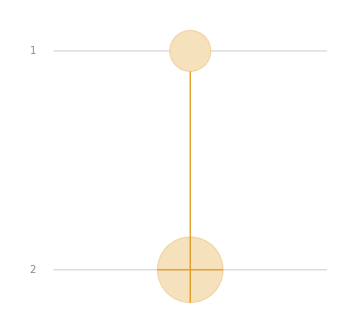

```mathematica
QuantumOperator[{"CNOT"->{1,2}}]//TraditionalForm(*模2加法*)
QuantumCircuitOperator["CNOT"]//TraditionalForm
```

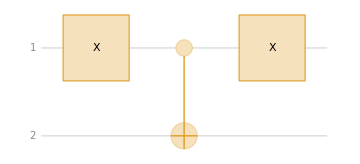

```mathematica
QuantumCircuitOperator[{"X","CNOT","X"}]//TraditionalForm
```

-Graphics-

#### 交换门

0000+0110+1001+1111

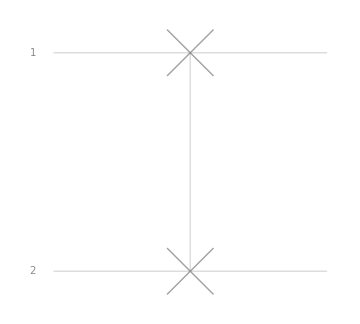

```mathematica
QuantumOperator["SWAP"]//TraditionalForm
QuantumCircuitOperator["SWAP"]//TraditionalForm
```

#### SWAP门拆成三个CNOT门

```mathematica
QuantumCircuitOperator[{"CNOT"->{1,2},"CNOT"->{2,1},"CNOT"->{1,2}}]==QuantumCircuitOperator["SWAP"]
```

True

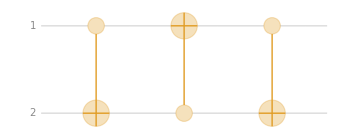

```mathematica
QuantumCircuitOperator[{QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,1}],QuantumOperator["CNOT",{1,2}]}]["Diagram"]
```

```mathematica
QuantumCircuitOperator["SWAP"]["Diagram"]
```

-Graphics-

#### Toffoli 门 和 测量

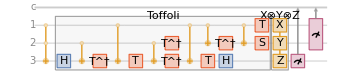

```mathematica
QuantumCircuitOperator[{QuantumOperator[…],QuantumCircuitOperator["Toffoli"],QuantumCircuitOperator[{"XYZ"}],QuantumMeasurementOperator["X",{3}],QuantumMeasurementOperator["X",{1,2}]}]["Diagram"]
```

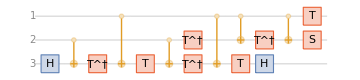

```mathematica
QuantumCircuitOperator["Toffoli"]["Diagram"]
```

```mathematica
tfl[a_,b_,c_]:={a,b,Mod[c+a b,2]}
```

```mathematica
QuantumOperator[…]["Matrix"]//Normal//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

#### CZ门

-Graphics-

```mathematica
QuantumOperator[{"Z"->{1,2}}]//TraditionalForm
QuantumOperator[{"Z"->{2,1}}]//TraditionalForm
```

0000-0101-1010+1111

0000-0101-1010+1111

#### 一般的受控U门，单比特控制单比特

-Graphics-

-Graphics-

X是泡利X矩阵

-Graphics-

-Graphics-

-Graphics-

#### 量子线路的特性

不出现回路，无环

不允许扇入扇出，扇入不可逆，扇出是量子克隆

## 1.3 测量

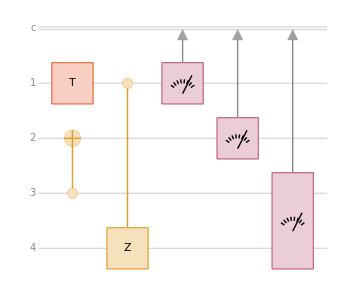

```mathematica
qc=QuantumCircuitOperator[{"T","CNOT"->{3,2},"CZ"->{1,4},{1},{2},{3,4}}];
%//TraditionalForm
```

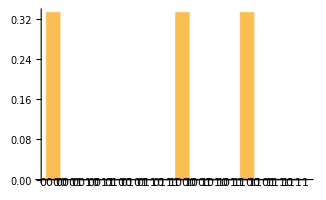

<|0000→0000,1000→ⅇ^((ⅈ π)/4) 1000,1100→ⅇ^((ⅈ π)/4) 1100|>

```mathematica
qc@QuantumState[{1,0,1,1}];
%["ProbabilityPlot"]
%%["StateAssociation"]//TraditionalForm
```

#### 延迟测量原理与经典的if-then语句

-Graphics-

-Graphics-

-Graphics-

```mathematica
inis=(QuantumCircuitOperator["HH"]@QuantumState[{1,0,0,0}])["Normalized"];
%//TraditionalForm
```

00/2+01/2+10/2+11/2

左侧

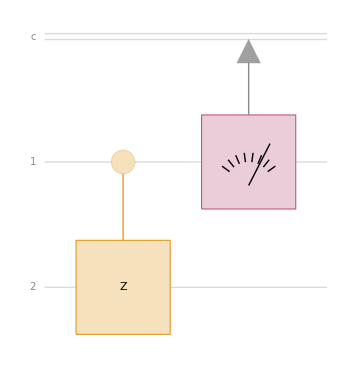

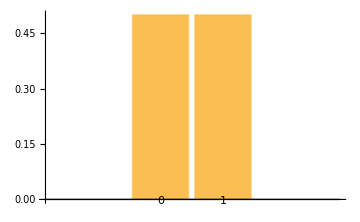

<|0→00/2+01/2,1→10/2-11/2|>

```mathematica
qc1=QuantumCircuitOperator[{"CZ",{1}}];
qc1//TraditionalForm
qmr=qc1@inis;
qmr["ProbabilityPlot"]
dst=qmr["Distribution"][[1,1]];
qmr["StateAssociation"];
%//TraditionalForm
```

```mathematica
Normal[#["Normalized"]["DensityMatrix"]]&/@qmr["StateAssociation"]//Values(*测量后的态*)
dst.%//MatrixForm
```

{{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1/2,-1/2},{0,0,-1/2,1/2}}}

(1/4 | 1/4 | 0 | 0
1/4 | 1/4 | 0 | 0
0 | 0 | 1/4 | -1/4
0 | 0 | -1/4 | 1/4)

右侧

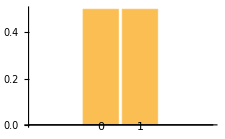

<|0→00/2+01/2,1→10/2+11/2|>

```mathematica
qmr1=QuantumMeasurementOperator[{1}]@inis;
qmr1["ProbabilityPlot"]
dst1=qmr1["Distribution"][[1,1]];
qmr1["StateAssociation"];
%//TraditionalForm
```

```mathematica
cz=QuantumOperator["CZ"]["Matrix"]//Normal
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}

```mathematica
Normal[#["Normalized"]["DensityMatrix"]]&/@qmr1["StateAssociation"]//Values(*测量后的态*)
dst1[[1]] %[[1]]+dst1[[2]] cz.%[[2]].ConjugateTranspose[cz]//TraditionalForm
```

{{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1/2,1/2},{0,0,1/2,1/2}}}

(1/4 | 1/4 | 0 | 0
1/4 | 1/4 | 0 | 0
0 | 0 | 1/4 | -1/4
0 | 0 | -1/4 | 1/4)

延迟测量的应用：利用Bell态隐形传态(teleportation)

设第1,2个比特是Alice的，而第3个比特是Bob的，双横线表示经典比特通信

方法 1

```mathematica
ops={QuantumOperator["CX"],QuantumOperator["H"],QuantumOperator["CX",{2,3}],QuantumOperator["CZ",{1,3}],QuantumMeasurementOperator[],QuantumMeasurementOperator[{2}]};
```

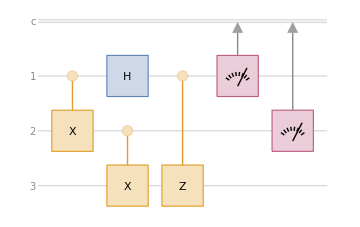

```mathematica
circuit=QuantumCircuitOperator[ops];
%["Diagram"]
```

```mathematica
QuantumCircuitOperator[{"CX","H","CX"->{2,3},"CZ"->{1,3},{1},{2}}]==circuit(*也可以用简写来构建线路*)
```

True

Alice的第一个比特ψ_0想要传给Bob，这个比特对Alice和Bob来说都是未知的，Alice的第二个比特和Bob的比特被制备在Bell态上

```mathematica
ψ0=QuantumTensorProduct[QuantumState[{α,β}],QuantumState["PhiPlus"]];
%["Formula"]
```

(α 000)/(√2)+(α 011)/(√2)+(β 100)/(√2)+(β 111)/(√2)

```mathematica
qss=circuit[ψ0]["StateAssociation"];
%//TraditionalForm
```

<|00→1/2 α 000+1/2 β 001,01→1/2 α 010+1/2 β 011,10→1/2 α 100+1/2 β 101,11→1/2 α 110+1/2 β 111|>

无论Alice的测量结果是什么，Bob手中的态都是ψ0

```mathematica
(QuantumPartialTrace[#,{1,2}]&/@qss)//TraditionalForm
```

<|00→1/4 α Conjugate[α] (00)+1/4 α Conjugate[β] (01)+1/4 β Conjugate[α] (10)+1/4 β Conjugate[β] (11),01→1/4 α Conjugate[α] (00)+1/4 α Conjugate[β] (01)+1/4 β Conjugate[α] (10)+1/4 β Conjugate[β] (11),10→1/4 α Conjugate[α] (00)+1/4 α Conjugate[β] (01)+1/4 β Conjugate[α] (10)+1/4 β Conjugate[β] (11),11→1/4 α Conjugate[α] (00)+1/4 α Conjugate[β] (01)+1/4 β Conjugate[α] (10)+1/4 β Conjugate[β] (11)|>

方法2：LOCC ( local operations and classical communication )

Alice在本地执行一系列的逻辑门和测量，将测量结果告诉Bob

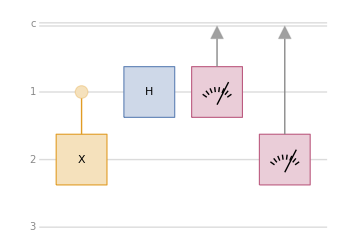

```mathematica
qco2=QuantumCircuitOperator[{"I"->3,{"CX"},"H",{1},{2}}];
qco2["Diagram"]
```

Bob根据Alice的测量结果对自己的态作用逻辑门以得到正确的ψ0

```mathematica
qss2=qco2[ψ0]["StateAssociation"];(*没有正确的归一化*)
%//TraditionalForm
```

<|00→1/2 α 000+1/2 β 001,01→1/2 β 010+1/2 α 011,10→1/2 α 100-1/2 β 101,11→-1/2 β 110+1/2 α 111|>

```mathematica
QuantumOperator["X",3]@qss2[[2]]//TraditionalForm
-QuantumOperator["Z",3]@qss2[[3]]//TraditionalForm
-QuantumOperator["X",3]@QuantumOperator["Z",3]@qss2[[4]]//TraditionalForm
```

1/2 α 100+1/2 β 101

1/2 α 100+1/2 β 101

1/2 α 000+1/2 β 001

信息的传递就是物质的传递

#### 隐含测量原理

-Graphics-

-Graphics-

在分析量子算法时带来一些便利。

#### Bell 基的测量

从计算基中的态获得Bell 态

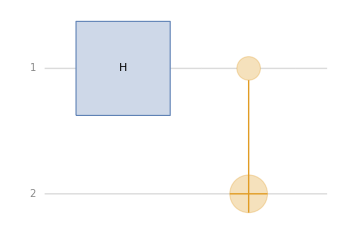

```mathematica
qco=QuantumCircuitOperator[{"H","CNOT"}];
qco["Diagram"]
```

```mathematica
TableForm[{QuantumBasis[{2,2}]["Names"],TraditionalForm/@qco/@(QuantumBasis[{2,2}]["PureStates"]),#["Formula"]&/@(QuantumState[#,QuantumBasis["Bell"]]&/@(qco/@(QuantumBasis[{2,2}]["PureStates"])))}//Transpose,TableHeadings->{{1,2,3,4},{"输入","输出"}}]
```

| 输入 | 输出 | 
1 | 00 | 00/(√2)+11/(√2) | Φ^+
2 | 01 | 01/(√2)+10/(√2) | Ψ^+
3 | 10 | 00/(√2)-11/(√2) | Φ^-
4 | 11 | 01/(√2)-10/(√2) | Ψ^-

-Graphics-

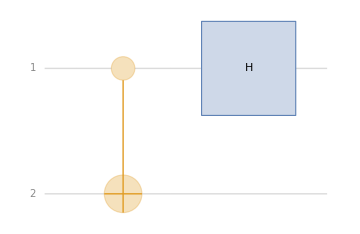

```mathematica
qco1=QuantumCircuitOperator[{"CNOT","H"->1}];
qco1["Diagram"]
qco1["Matrix"]//Normal//MatrixForm;
```

```mathematica
b22=QuantumState/@Flatten/@QuantumBasis[2,2]["Elements"];
qco1["Dagger"]/@%;
```

```mathematica
TableForm[{b22,qco1["Dagger"]/@b22,#["Formula"]&/@(QuantumState[#,QuantumBasis["Bell"]]&/@(qco/@(QuantumBasis[{2,2}]["PureStates"])))}//Transpose,TableHeadings->{{1,2,3,4},{"仪器读数","实际基底"}}]//TraditionalForm
```

| 仪器读数 | 实际基底 | 
1 | 00 | 00/(√2)+11/(√2) | Φ^+
2 | 01 | 01/(√2)+10/(√2) | Ψ^+
3 | 10 | 00/(√2)-11/(√2) | Φ^-
4 | 11 | 01/(√2)-10/(√2) | Ψ^-

两个矩阵的关系？

-Graphics-

```mathematica
qco["Matrix"]//Normal//MatrixForm
```

(1/(√2) | 0 | 1/(√2) | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0 | -1/(√2)
1/(√2) | 0 | -1/(√2) | 0)

```mathematica
qco1["Dagger"]["Matrix"]//Normal//MatrixForm
```

(1/(√2) | 0 | 1/(√2) | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0 | -1/(√2)
1/(√2) | 0 | -1/(√2) | 0)

#### 对算符 U进行测量

习题 4.34 既要概率分布又要测量后的态

-Graphics-

-Graphics-

既幺正又厄米，有多特殊？

-Graphics-

```mathematica
$Assumptions={x,y,z}∈Sphere[];
```

```mathematica
u=x PauliMatrix[1]+y PauliMatrix[2]+z PauliMatrix[3];
vu=((Normalize/@Eigensystem[u][[2]])//FullSimplify)/.Sign[x+ⅈ y]->(x+I y)/Abs[x+ⅈ y]/.Abs[x+ⅈ y]->√(x^2+y^2)//FullSimplify//Conjugate//Reverse//Simplify
vu.u.ConjugateTranspose[vu]/.x^2+y^2->1-z^2//FullSimplify//Chop
```

{{(√((x^2+y^2) (1+z)))/(√2 (x-ⅈ y)),(√(1-z))/(√2)},{((-1+z) √(1+z))/(√2 (x-ⅈ y)),(√(1+z))/(√2)}}

{{1,0},{0,-1}}

```mathematica
u.(Conjugate@vu)[[1]]-(Conjugate@vu)[[1]]//Chop//FullSimplify(*Eigenvectors返回以本征值为行向量的矩阵，不需要做任何的转置或共轭*)
```

{-((-1+z) (√(1-z)+√(1-z) z-√((x^2+y^2) (1+z))))/(√2 (x+ⅈ y)),-(√(1-z)+√(1-z) z-√((x^2+y^2) (1+z)))/(√2)}

题目中的设计方案

```mathematica
U=QuantumOperator[u,"Label"->"U","Color"->"Red"];
```

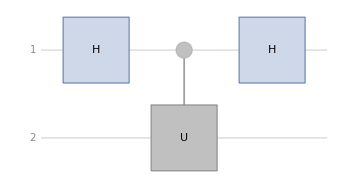

```mathematica
c1=QuantumCircuitOperator[{"H",QuantumOperator[KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]]+KroneckerProduct[{{0,0},{0,1}},u]]->{1,2},"H"}];
c1=QuantumCircuitOperator[{"H",QuantumOperator[{"Controlled",U},{1,2}],"H"}];
c1//TraditionalForm
```

直接的设计方案

-Graphics-

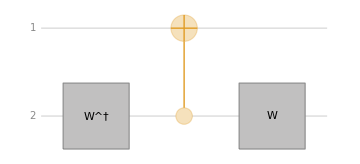

```mathematica
c2=QuantumCircuitOperator[{QuantumOperator[vu,"Label"->"W^†"]->2,"CNOT"->{2,1},QuantumOperator[ConjugateTranspose[vu],"Label"->"W"]->2}];
c2//TraditionalForm
```

```mathematica
m1=c1["Matrix"]//Normal//FullSimplify;
m2=c2["Matrix"]//Normal//FullSimplify;
%-%%//FullSimplify//Chop(*检验两种设计是相同的*)
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

直接设计方案的推广：多比特，测量 σ_x⊗σ_z⊗σ_z⊗σ_x⊗"I"

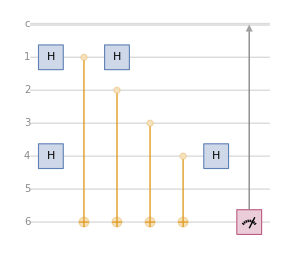

## 1.4 通用量子门

通用门

经典通用门 ：与或非

量子通用门的定义：通过矩阵乘法和张量积，能够以任意的精度逼近任意量子线路 U(2^n) 的一组逻辑门

矩阵乘法和张量积都对应物理上可实现的操作

通用门的集合

单位门，恒等变换 I

阿达玛门 H

受控非门 CNOT

相位门 S ( S = √Z )

T门，又称 π/8 门 ( T = √S )

称 H, CNOT, S, T 是一组通用门，记作 U ∈ , 任取幺正算符U

通用门中真正发挥量子优势的关键元素：T = diag( 1 , e^(iπ/4))

-Graphics-

Gottesman-Knill 定理：Clifford群元生成的量子线路可以被经典计算机高效模拟( 多项式时间  )。

T 不属于 Clifford群。

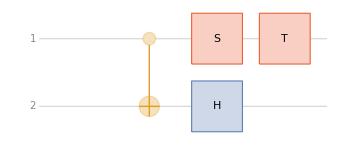

{00+11,0000+0101+1011+1110,00/(√2)+01/(√2)+10/(√2)-11/(√2),00+ⅈ (11),00+ⅇ^((ⅈ π)/4) (11)}

```mathematica
uni=QuantumCircuitOperator[{"I","CNOT","H"->2,"S","T"}];
uni//TraditionalForm
uni["Operators"]//TraditionalForm
```

证明通用性的步骤三步走

1. 任何幺正变换都可以拆成二级幺正变换 ( 二级幺正变换 ：非平凡子空间维度为2的幺正变换，即不变子空间是 N -2 = 2^n-2 维的  )

2. 利用第一步的结果，证明任意幺正算符都可以用单比特门和CNOT门精确实现

3. 证明单比特门可以用H, S, T门以任意精度逼近

其他问题

逼近效率

其他通用门

Toffoli 门 + H门

两个方向的旋转 + S门，CNOT门

Clifford 门( CNOT, H, S ) + T 门 (非Clifford门)

### STEP 1 二级幺正门是通用的 STEP 2 单比特门和CNOT门是通用的 STEP 3 H，T，CNOT门是通用的

-Graphics-

举例：

```mathematica
QuantumOperator[{"Controlled",{{"u_00","u_01"},{"u_10","u_11"}}},{1,2}]["Matrix"]//Normal//MatrixForm
QuantumOperator["CNOT",{1,2}]["Matrix"]//Normal//MatrixForm
QuantumOperator["Toffoli"]["Matrix"]//Normal//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | u_00 | u_01
0 | 0 | u_10 | u_11)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
(*images=Import/@{"D:\\WeChat Files\\wxid_rzkeqfbjyqqp12\\FileStorage\\File\\2023-11\\量子计算习题\\量子计算习题-277.jpg","D:\\WeChat Files\\wxid_rzkeqfbjyqqp12\\FileStorage\\File\\2023-11\\量子计算习题\\量子计算习题-278.jpg","D:\\WeChat Files\\wxid_rzkeqfbjyqqp12\\FileStorage\\File\\2023-11\\量子计算习题\\量子计算习题-279.jpg","D:\\WeChat Files\\wxid_rzkeqfbjyqqp12\\FileStorage\\File\\2023-11\\量子计算习题\\量子计算习题-280.jpg","D:\\WeChat Files\\wxid_rzkeqfbjyqqp12\\FileStorage\\File\\2023-11\\量子计算习题\\量子计算习题-281.jpg","D:\\WeChat Files\\wxid_rzkeqfbjyqqp12\\FileStorage\\File\\2023-11\\量子计算习题\\量子计算习题-282.jpg"};*)
```

以下的过程，参考3

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

### 复杂性

对于单比特门，有Solovay–Kitaev 定理：S是SU(2)的子集，满足  蕴含 g^-1∈S，且，则以精度 ϵ  逼近任意的 U∈SU(2) 需要  个 S中的门

对于多比特门，Nielsen p.200：逼近一般的幺正变换是困难的，存在一些态，从计算基 0 态出发，需要-Graphics-个门才能达到。

精度越高，所需的门越多。

-Graphics-

## 1.5 量子计算机的要素

量子线路模型( 量子计算机 )的关键要素4

执行经典计算的能力

态初始化的能力，将n个qubit初始化到|0...0

准确执行逻辑门的能力 ( 抵抗噪声 )

在计算基下测量的能力

其他要素

在两台计算机 ( 两个量子处理单元 ) 之间传输量子信息的能力

## 2 其他量子计算模型

## 3 量子系统的模拟

工程领域的模拟：以在COMSOL中进行多物理场仿真模拟的一般流程为例

定义几何模型，设置材料属性，定义了物态方程

选择物理场： 热传导、电场、磁场、流体流动等。Comsol支持多个物理场耦合的仿真。确定物理过程满足的动力学方程，通常是复杂的PDE。

定义边界条件： 设置模型的边界条件，这包括指定固定边界、施加力或流量、设定热通量等。

网格划分： 对几何模型进行网格划分，将其离散为小元素，以便进行数值求解。

设定求解器选项： 选择适当的求解器和求解选项。

运行仿真： 启动仿真计算，Comsol 将求解所选物理场的方程，并提供关于模型行为的详细信息。

分析和解释结果

量子领域的(经典)近似计算方法5-6

量子力学

半经典近似，包括WKB近似等，动机：ℏ 趋于零时粒子行为回到经典情形。关于ℏ 做泰勒展开，舍去高阶项7

微扰论，包括简并微扰、非简并微扰和含时微扰

-Graphics-

变分法：数值求解能量本征值和本征态的方法

绝热近似和突变近似，H(t)变化缓慢、快速

线性响应理论：当处于平衡状态的物理系统受到外部扰动时，它就会脱离平衡。一般来说，可观测量的期望可以非线性地依赖于外部扰动，但如果扰动很弱，则只需要保持外部扰动中的一阶（线性）项，并且可以在平衡状态下计算外部扰动的一次方之前的系数

凝聚态物理：量子多体计算，电子(能带)结构、物性(电磁、输运性质等)计算

随着Hilbert空间维度增长，经典计算机上模拟量子系统开销指数上升，简单介绍：8

-Graphics-

尤里·伊万诺维奇·马宁（俄：Ю́рий Ива́нович Ма́нин；1937年2月16日－2023年1月7日）是一位俄罗斯数学家，以代数几何和丢番图几何方面的工作以及从数理逻辑到理论物理的许多著作而闻名。1980 年，他通过著作《可计算和不可计算》成为最早提出量子计算机想法的人之一。

精确对角化：指数墙，其余方法都是在攻克指数墙

Born-Oppenheimer 近似：电子与核解耦合

密度泛函理论与Kohn-Sham方程：将体系的电子密度而不是波函数，视为基本变量，简化了处理多体量子系统的复杂性。

数值重整化群：解决大量一维量子模型(如海森堡模型、哈伯德模型、近藤及安德森格点模型等〉的基态、低能激发、谱函数及含时动力学演化

量子蒙特卡洛9

动力学平均场

还有很多 丶丶丶

高能物理

关于耦合常数的幂次展开：典型流程是确定拉氏量和参与反应的粒子→费曼图→微分散射截面→散射截面

非微扰方法：格点QCD

量子模拟算法：量子计算的重要应用

费曼：用遵循量子力学原理的量子力学元件来制作计算机10。

让一个可控的、较容易处理的量子系统来模拟其他复杂的量子系统或经典系统的行为

-Graphics-

量子计算利用了量子力学本身的原理，具有经典计算机所不具备的高效模拟量子系统的潜力，帮助我们避免爆炸，从量子层面推倒量子指数墙。

量子模拟的潜在应用领域：凝聚态、高能物理、量子化学、宇宙学、核物理学、经典物理11。

三分类12

Digital quantum simulation (Nielsen)：基于量子线路模型

Analog quantum simulation

Quantum-information-inspired algorithms for the classical simulation of quantum systems

由第一小节，原则上，通用量子计算机可以实现任何系统的任何幺正演化，但并非都能高效模拟，因此对某个或某类哈密顿量找到高效模拟的方法是一项重要而富于挑战性的任务。

### 量子模拟 例1

总哈密顿量是局域相互作用哈密顿量的和，凝聚态中的一大类模型( Hubbard, Ising )

-Graphics-

将演化时间 t 拆成多段，每段为 Δt ，总演化是每段演化的相继作用。

-Graphics-

利用 Trotter 公式将每小段演化进一步拆成局域哈密顿量演化的相继作用

-Graphics-

上式中的每个因子都是局域的幺正演化，可以( 或许？)被高效模拟

#### BCH公式及其对偶

-Graphics-

-Graphics-

对偶形式

-Graphics-

#### Trotter公式

考虑哈密顿量被拆成两项的情形

-Graphics-

-Graphics-

#### 更多的矩阵指数相关公式

即 ，其中 ，

-Graphics-

### 量子模拟 例2

-Graphics-

```mathematica
etz=QuantumOperator[MatrixExp[-I Δt PauliMatrix[3]],"Label"->"e^(-iΔt Z)"];
```

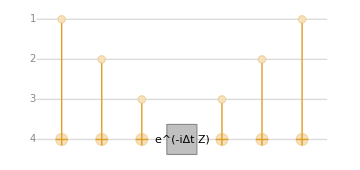

```mathematica
qs=QuantumCircuitOperator[{"CNOT"->{1,4},"CNOT"->{2,4},"CNOT"->{3,4},etz->4,"CNOT"->{3,4},"CNOT"->{2,4},"CNOT"->{1,4}}];
qs//TraditionalForm
```

```mathematica
qbls=QuantumState[#]&/@StringJoin@@@((ToString/@Flatten[{#,0}])&/@Tuples[{0,1},3]);
qbls//TraditionalForm
```

{0000,0010,0100,0110,1000,1010,1100,1110}

```mathematica
qs[#]&/@qbls//TraditionalForm
```

{ⅇ^(-ⅈ Δt) 0000,ⅇ^(ⅈ Δt) 0010,ⅇ^(ⅈ Δt) 0100,ⅇ^(-ⅈ Δt) 0110,ⅇ^(ⅈ Δt) 1000,ⅇ^(-ⅈ Δt) 1010,ⅇ^(-ⅈ Δt) 1100,ⅇ^(ⅈ Δt) 1110}

## 4 总结：需要记住的关键知识点

单比特门U(2)都可以视为qubit生活的空间的旋转，旋转可以一次实现，也可以通过欧拉角分三次实现。

隐含测量原理。推迟测量原理。对算符 U 的测量

通用门的定义。H, T, CNOT构成一组通用门

一般的量子门 U(2^n) 不能高效实现

Trotter分解公式与量子模拟

## 5 参考文献

1	https://www.wikiwand.com/en/Plate_trick

2	https://www.youtube.com/watch?v=ACZC_XEyg9U

3	Mathematics Of Quantum Computing An Introduction by Wolfgang Scherer

4	https://arxiv.org/pdf/cond-mat/9612126v2.pdf

5	中国科学发展战略 计算物理学 科学出版社

6	Ideas of Quantum Chemistry Lucian Piela

7	@book{RN11605,
   author = {Band, Yehuda B and Avishai, Yshai},
   title = {Quantum mechanics with applications to nanotechnology and information science},
   publisher = {Academic Press},
   ISBN = {0444537872},
   year = {2013},
   type = {Book}
}

8	宝宝的量子信息学 - Quantum information for babies Chris Ferrie

9	Ma, N., Sandvik, A. W., & Yao, D. X. (2014). Criticality and Mott glass phase in a disordered two-dimensional quantum spin system. Physical Review B, 90(10), 104425.

10	Feynman, R.P., 2018. Simulating physics with computers. Int. j. Theor. phys, 21(6/7).

11	Sinha, S., and P. Russer, 2010, Quantum computer algorithm for electromagnetic field simulation," Quant. Inf.Process. 9, 385.

12	@article{RN398,
   author = {Georgescu, I.  M and Ashhab, S. and Nori, Franco},
   title = {Quantum simulation},
   journal = {Reviews of Modern Physics},
   volume = {86},
   number = {1},
   pages = {153-185},
   ISSN = {0034-6861},
   DOI = {10.1103/revmodphys.86.153},
   url = {https://dx.doi.org/10.1103/revmodphys.86.153},
   year = {2014},
   type = {Journal Article}
}